# ЛР1. Актуализация знаний 1-ого семестра.

## 1. Работаем со списками и элементарными вычислениями.

### 1.1

Докажите эмпирически (с помощью вычислений) сходимость числового ряда ∑_(n=0)^∞ (-1)^n/(2n+1).  Сделайте предположение о том, к какому числу сходится ряд. Подтвердите вычисления графически.

### 1.2

Докажите эмпирически расходимость  ряда. ∑_(n=1)^∞ 1/n. Для этого можно доказать, что для любого числа K, существует N, такое что ∑_(n=1)^N 1/n> K.

### Пример

```mathematica
1/(#!)&/@Range[0,30](*Первый 31 член ряда*)
```

{1,1,1/2,1/6,1/24,1/120,1/720,1/5040,1/40320,1/362880,1/3628800,1/39916800,1/479001600,1/6227020800,1/87178291200,1/1307674368000,1/20922789888000,1/355687428096000,1/6402373705728000,1/121645100408832000,1/2432902008176640000,1/51090942171709440000,1/1124000727777607680000,1/25852016738884976640000,1/620448401733239439360000,1/15511210043330985984000000,1/403291461126605635584000000,1/10888869450418352160768000000,1/304888344611713860501504000000,1/8841761993739701954543616000000,1/265252859812191058636308480000000}

```mathematica
1/(#!)&/@Range[0,30]//Total//N[#,30]&(*Частичная сумма первых 31 члена*)
```

2.71828182845904523536028747135

```mathematica
ⅇ-(1/(#!)&/@Range[0,30]//Total//N[#,30]&)(*Предполагаем, что ряд сходится к экпоненте*)
```

0.

```mathematica
Table[Abs[ⅇ-(1/(#!)&/@Range[0,i]//Total)],{i,1,30}]//N[#,50]&(*смотрим, как погрешность изменяется с увеличением количества членов ряда*)
```

{0.71828182845904523536028747135266249775724709369996,0.21828182845904523536028747135266249775724709369996,0.051615161792378568693620804685995831090580427033293,0.0099484951257119020269541380193291644239137603666262,0.0016151617923785686936208046859958310905804270332929,0.00022627290348967980473191579710694220169153814440402,0.000027860205076981392033503098694243788993125445991321,3.0586177753940904462015113926564874058238586897337×10^-6,3.0288585299550138094577947025789834056812676733511×10^-7,2.7312660755642474420206278018039434042553575095249×10^-8,2.2605523702007556451541696325977152675014667098074×10^-9,1.7287667141394574723316060047757203624712434435396×10^-10,1.2286233045729601239236828776022556919867239319076×10^-11,8.1548744799987652538513079734045125363458895944194×10^-13,5.0771074817894877795017598761644209219078935466305×10^-14,2.9763014940210248206355238504687689431095589678282×10^-15,1.6484423967550405743657826745844892687606623262366×10^-16,8.6521699896417928144146239578755926408721917789627×10^-18,4.3153474301746309745864272100331189165145278713657×10^-19,2.0502980686246611610843659159697854190415837545263×10^-20,9.3003962285535037999608478619242383512836375520102×10^-22,4.0360483610293051321195041942177000797114946561826×10^-23,1.6787819039862109440259226269488775653215200992528×10^-24,6.7044332890092594977209322147705763996793996645543×10^-26,2.5748300462478610152607899556588919438049525412535×10^-27,9.5233783023063555185846409810935326382296998780863×10^-29,3.396884385108093701589241446196192403680126837431×10^-30,1.1699514803825579143719971888408047587238141087988×10^-31,3.8955191737786221216120731146973059479763961712231×10^-33,1.2553154496271647775915158905120028382956234760113×10^-34}

## 2. Пишем собственные функции.

### Вычисление числа π методом Монте-Карло. Теория.

Идея метода в случайном распределении точек. Зададим некторое количество случайных точек в квадрате 0 ≤ x ≤ 1, 0 ≤ y ≤ 1.

```mathematica
Short[pts=RandomReal[{0,1},{1000,2}]]
```

{{0.212362,0.0245773},{0.629635,0.168682},«996»,{0.316012,0.0759074},{0.286442,0.0949814}}

Очевидно, что геометрически точки будут лежать внутри квадарата со строной 1. Если вписать в этот квадрат окружность, то логично, что часть точек окажется в ней.

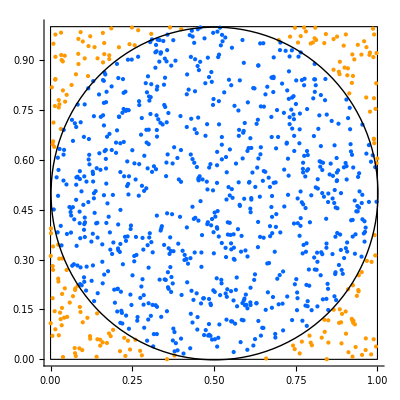

Далее логично предположить, что отношение площадей фигур будет “равно” или, лучше сказать, “близко”, отношению количества точек внутри каждой фигуры. 
Тогда если K - это количество точек в круге, а N - общее количество точек  (лежащих в квадрате), то K/N=S_круга/S_квадарата. 
Площади круга и квадарта мы можем вычислить. S_круга=π*1/4, S_квадрата=1.  
Получаем финальное соотношение, откуда выражаем π. π = 4 * K/N.

Остаётся только найти количечество точек внутри окуржности исходя из геометрических свойств. С увеличением количества точек, ожидаем увеличение точности.

### 2.1

Реализуйте функцию для вычисления числа π методом Монте-Карло. На вход функция принимает, количество точек. Исследуйте, как меняется точность вычислений с увеличением количества точек.

## 3. Вспоминаем графические примитивы.

Модифицируйте функцию из задания 2.1 таким образом, чтобы она также возвращала графическую визуализацию работы метода.

## 4. Динамические вычисления.

### 4.1.

Реалиузйте функцию принмиающую на вход полином и возвращающую все его корни, а также графическую интерпретацию эдействительных корней.

### Пример.

Пусть задано уравнение.

```mathematica
eqn = x^7+7 x^3+x^2+11==0
```

11+x^2+7 x^3+x^7==0

```mathematica
eqn//Solve//Values//N//Flatten(*получили корни*)
```

{-1.12547,-1.14624-1.26951 ⅈ,-1.14624+1.26951 ⅈ,0.455814-1.03462 ⅈ,0.455814+1.03462 ⅈ,1.25316-1.0214 ⅈ,1.25316+1.0214 ⅈ}

```mathematica
rootsreal=eqn//Solve//Values//N//Flatten//Cases[#,_Real]&(*вот так можно получить дествительные корни*)
```

{-1.12547}

Для получение визуализации лучше использовать функцию Plot с опцией Epilog.

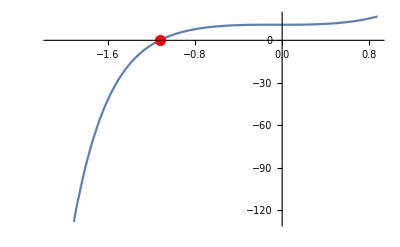

### 4.2

Реализуйте с помщью функции Manipulate скрипт аналогичный предыдущему. Теперь один из коэффициентов полинома - параметр. Продемонстируйте изменения графической интерпретации при изменении параметра.

```mathematica
x^7+7 x^3+a*x^2+11==0
```

### 4.3

Реалиузйте функцию принмиающую на вход полином и возвращающую все его корни, а также графическую интерпретацию комплексных корней. Комплексные корни стоит отрисовать на комплексной плоскости.  Подпишите их.

```mathematica
rootscomplex=eqn//Solve//Values//N//Flatten//Cases[#,_Complex]&
```

{-1.14624-1.26951 ⅈ,-1.14624+1.26951 ⅈ,0.455814-1.03462 ⅈ,0.455814+1.03462 ⅈ,1.25316-1.0214 ⅈ,1.25316+1.0214 ⅈ}